## Analysis of Fussmann (Science 2000) Data

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/hopf_fussmann_2000"];
```

```mathematica
(* get package for user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Import Data

```mathematica
(* Import raw data *)
raw=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/hopf_fussmann_2000/data/raw_fussmann_2000.xls"][[1]];
```

```mathematica
(* Sneak peek *)
raw[[1;;10]]//TableForm
```

[mio cells/mL] | [mio cells/mL] | [1/mL] | [1/mL] | [1/day] | [1/day] |  | 
Chlorella | Chlorella-error | Brachionus | Brachionus-error | delta | meandelta | day# | chemostat
1.4164 | 0.0102 | 8.2 | 0.4 | 0.0367199 | 0.0394451 | 20. | 5p4
1.4001 | 0.0099 | 10.25 | 0.25 | 0.0339663 | 0.0394451 | 21. | 5p4
1.3685 | 0.028 | 8.4 | 1.8 | 0.0408107 | 0.0394451 | 22. | 5p4
1.2441 | 0.0081 | 10. | 0. | 0.0379307 | 0.0394451 | 23. | 5p4
1.208 | 0.0884 | 9.61364 | 0.613636 | 0.0382543 | 0.0394451 | 24. | 5p4
1.2077 | 0.0039 | 7.8 | 1.8 | 0.0371382 | 0.0394451 | 25. | 5p4
1.04635 | 0.02745 | 8.4 | 0.2 | 0.037249 | 0.0394451 | 26. | 5p4
1.01259 | 0.03521 | 8. | 1. | 0.0345425 | 0.0394451 | 27. | 5p4

```mathematica
(* select desired columns and data (deltamean, time, chlorella, brachionus) *)
raw2=raw[[3;;,{6,7,1,3}]];
```

```mathematica
(* display *)
raw2[[1;;10]]//TableForm
```

0.0394451 | 20. | 1.4164 | 8.2
0.0394451 | 21. | 1.4001 | 10.25
0.0394451 | 22. | 1.3685 | 8.4
0.0394451 | 23. | 1.2441 | 10.
0.0394451 | 24. | 1.208 | 9.61364
0.0394451 | 25. | 1.2077 | 7.8
0.0394451 | 26. | 1.04635 | 8.4
0.0394451 | 27. | 1.01259 | 8.
0.0394451 | 28. | 0.9995 | 8.4
0.0394451 | 29. | 1.05143 | 6.1

### Partition data sets by delta values

```mathematica
(* Union of delta values *)
deltaVals=Union[raw[[3;;,6]]];
deltaVals
```

{0.0394451,0.0702468,0.121966,0.320281,0.643073,0.671744,0.689799,0.892307,0.950811,0.996124,1.14576,1.16675,1.24268,1.3686}

```mathematica
(* create dataSet ordered as {deltaVal,{tVals,Chlorella,Brachionus}} *)
dataSet1=Table[Cases[raw2,{deltaVals[[i]],_,_,_}][[;;,{2,3,4}]],{i,1,Length[deltaVals]}];
```

```mathematica
(* set time to start at t=0 for each trial *)
dataSet=dataSet1;
For[i=1,i≤Length[deltaVals],i++,
dataSet[[i,;;,1]]=dataSet1[[i,;;,1]]-dataSet1[[i,1,1]];
]
```

```mathematica
dataSet//Dimensions
```

{14}

```mathematica
(* export dataSet as a mat file ( can store multidimensional arrays ) *)
Export["data_export/seriesData.mat",dataSet];
```

```mathematica
(* Union of chemostats *)
chemoStats=Union[raw[[3;;,8]]]
```

{5b2,5b3high,5b3low,5g2,5o2,5o3high,5o3low,5ohigh,5olow,5p4,5r3,5y3high,5y3low,tan}

#### 5b3

```mathematica
(* (time, chlor, brach, delta, chemostat *)
data5b3=Join[Cases[raw,{_,_,_,_,_,_,_,"5b3low"}][[;;,{7,1,3,6,8}]],
Cases[raw,{_,_,_,_,_,_,_,"5b3high"}][[;;,{7,1,3,6,8}]]];
```

```mathematica
(* change from delta = 1.24 -> 1.37 - time gap of 21 *)
```

#### 5o3

```mathematica
(* (time, chlor, brach, delta, chemostat *)
data5o3=Join[Cases[raw,{_,_,_,_,_,_,_,"5o3low"}][[;;,{7,1,3,6,8}]],
Cases[raw,{_,_,_,_,_,_,_,"5o3high"}][[;;,{7,1,3,6,8}]]];
```

```mathematica
data5o3//TableForm;
```

```mathematica
(* change from delta = 0.12->0.32 - time gap of 13 *)
```

#### 5o

```mathematica
(* (time, chlor, brach, delta, chemostat *)
data5o=Join[Cases[raw,{_,_,_,_,_,_,_,"5ohigh"}][[;;,{7,1,3,6,8}]],
Cases[raw,{_,_,_,_,_,_,_,"5olow"}][[;;,{7,1,3,6,8}]]];
```

```mathematica
data5o//TableForm;
```

```mathematica
(* change from delta = 1.14->0.95 -  no time gap - change at  - good for analysing Hopf *)
```

#### 5y3

```mathematica
(* (time, chlor, brach, delta, chemostat *)
data5y3=Join[Cases[raw,{_,_,_,_,_,_,_,"5y3high"}][[;;,{7,1,3,6,8}]],
Cases[raw,{_,_,_,_,_,_,_,"5y3low"}][[;;,{7,1,3,6,8}]]];
```

```mathematica
data5y3//TableForm;
```

```mathematica
(* change from delta = 0.67->0.07  -  time gap 41 *)
```

## Plot Data

```mathematica
(* plot parameters *)
padding={{50,50},{50,30}};
tmax=130;
```

```mathematica
(* statistical metrics *)
```

```mathematica
(* Plot of prey (chlorella) *)
Clear[plotChlorella]
plotChlorella[i_]:=ListLinePlot[dataSet[[i,;;,{1,2}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)","Brachionus (females/ml)"},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->300,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,tmax},{0,5}},
Epilog->Text[Style["δ= "<>ToString[NumberForm[deltaVals[[i]],{3,2}]],14],Scaled[{0.15,1.1}]],
PlotRangeClipping->False,
ImageSize->400];
```

```mathematica
(* Plot of predator (brachionus) *)
Clear[plotBrachionus]
plotBrachionus[i_]:=ListLinePlot[dataSet[[i,;;,{1,3}]],
Joined->True,
LabelStyle->14,
FrameLabel->{{"","Brachionus (females/ml)"},{"Time",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{None,Range[0,45,10]},{Automatic,None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->300,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,tmax},{0,40}}];
```

```mathematica
(* overlay the plots *)
Clear[joinPlot]
joinPlot[i_]:=Overlay[{plotChlorella[i],plotBrachionus[i]}]
```

```mathematica
Partition[Range[1,14],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

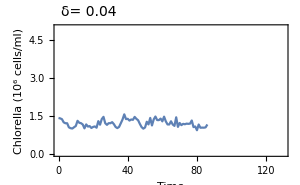
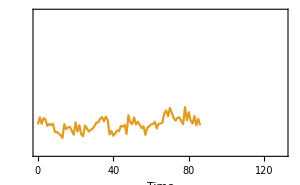
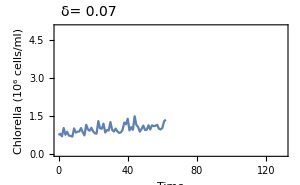
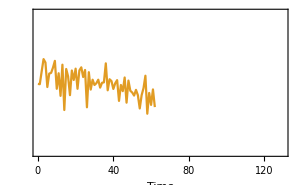
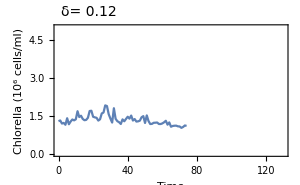
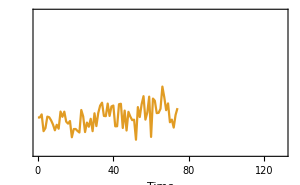
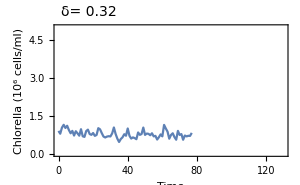
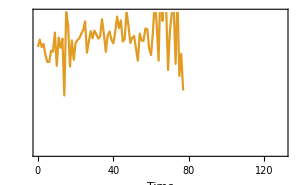
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- |

```mathematica
(* Display plots *)
plotDataFussmann=Grid[Partition[Table[joinPlot[i],{i,1,Length[deltaVals]}],UpTo[3]]]
```

```mathematica
(*Export["figures/empirical_tseries.png",plotDataFussmann,ImageResolution->200];*)
```

## Statistical Indicators

### Parameters

```mathematica
bandWidth=20; (* number of days *)
hamLength=40;
hamOffset=20;
```

```mathematica
(* make arrays to store metrics *)
fitPlotChlor=ConstantArray[0,Length[deltaVals]];
varChlor=ConstantArray[0,Length[deltaVals]];
cvarChlor=ConstantArray[0,Length[deltaVals]];
acChlor=ConstantArray[0,Length[deltaVals]];
psChlor=ConstantArray[0,Length[deltaVals]];
aicFoldChlor=ConstantArray[0,Length[deltaVals]];
aicHopfChlor=ConstantArray[0,Length[deltaVals]];
smaxChlor=ConstantArray[0,Length[deltaVals]];
cfChlor=ConstantArray[0,Length[deltaVals]];
lenChlor=ConstantArray[0,Length[deltaVals]];


fitPlotBrach=ConstantArray[0,Length[deltaVals]];
varBrach=ConstantArray[0,Length[deltaVals]];
cvarBrach=ConstantArray[0,Length[deltaVals]];
acBrach=ConstantArray[0,Length[deltaVals]];
psBrach=ConstantArray[0,Length[deltaVals]];
aicFoldBrach=ConstantArray[0,Length[deltaVals]];
aicHopfBrach=ConstantArray[0,Length[deltaVals]];
smaxBrach=ConstantArray[0,Length[deltaVals]];
cfBrach=ConstantArray[0,Length[deltaVals]];
lenBrach=ConstantArray[0,Length[deltaVals]];

(* array for psd plots *)
psPlots=ConstantArray[0,Length[deltaVals]];
```

### Function to detrend and compute EWS

```mathematica
Clear[ews]
ews[bandWidth_,yVals_,tVals_]:=
Module[{dataFit,len,dt,residuals,variance,mean,cvar,autoCorr,pSpec,aicFold,aicHopf,aicNull,smax,coherFactor,plot,output},
len=Length[yVals];
dt=tVals[[2]]-tVals[[1]];
(* Detrend t-series using Gaussian filtering - no filtering if bandwidth is zero, no filtering *)
If[bandWidth≠0,
dataFit=GaussianFilter[yVals,(*Length[dataSet[[1,;;,2]]]*)bandWidth];,
dataFit=ConstantArray[0,Length[yVals]];
];
(* make a plot *)
plot=ListLinePlot[{Transpose[{tVals,yVals}],Transpose[{tVals,dataFit}]},
ImageSize->250,
Frame->True,
LabelStyle->12,
FrameLabel->{{"Abundance",None},{"Time",None}},
PlotRange->All];
(* Find residual dynamics *);
residuals=yVals-dataFit;
(* Compute variance indicator *)
variance=Variance[residuals];
(* Compute mean of series *)
mean=Mean[yVals];
(* Compute coefficient of variation *)
cvar=variance/mean;
(* Compute lag-1 autocorrelation *)
autoCorr=CorrelationFunction[residuals,1];
(* Compute power spectrum *)
pSpec=TBPowerSpecWelch[{residuals,dt,hamLength,hamOffset}];
(* Compute AIC weight *)
{aicFold,aicHopf,aicNull}=TBFitSpec[pSpec,0.25];
(* Compute smax *)
smax=Max[pSpec[[2,;;]]];
(* Compute coherence factor *)
coherFactor=TBCoherFactor[pSpec];
(* Output *)
output={len,plot,variance,cvar,autoCorr,pSpec,aicFold,aicHopf,smax,coherFactor}
]
```

```mathematica
?TBFitSpec
```

TBFitSpec[pSpec] fits three power spectrum models to the input: unimodal, bimodal and flat (null).
pSpec = {freqVals,powerVals}
Outputs {foldWeight, hopfWeight, nullWeight}
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense);

```mathematica
?TBPowerSpecWelch
```

{freqVals,pSpec} = TBPowerSpecWelch[{yVals,dt,hamLength,hamOffset}] estimates the power spectrum usign Welch's method.
This involves computing the periodogram with overlapping Hamming windows.
hamLength: number of data points in Hamming window, or if in (0,1) taken as a proportion of total data input
hamOffset: number of data points to offset the window by on each interation, or if in (0,1) taken as a proportion of Hamming window size

### Function to plot PS and display EWS data

```mathematica
Clear[psPlot]
psPlot[i_,ωmax_]:=Grid[{{
ListLinePlot[Transpose[psChlor[[i]]],
PlotRange->{{-ωmax,ωmax},All},
Filling->Bottom,
AxesLabel->{"ω","S_chlor(ω)"},
LabelStyle->12,
ImageSize->300,
AspectRatio->1/2,
Epilog->{Text[Style["δ= "<>ToString[NumberForm[deltaVals[[i]],{3,2}]],12,Bold],Scaled[{0,0.95}],Left],
Text[Style["T= "<>ToString[lenChlor[[i]]],12],Scaled[{0,0.85}],Left],
Text[Style["Var= "<>ToString[NumberForm[varChlor[[i]],{3,2}]],12],Scaled[{1,0.95}],Right],
Text[Style["CV= "<>ToString[NumberForm[cvarChlor[[i]],{3,2}]],12],Scaled[{1,0.85}],Right],
Text[Style["AC(1)= "<>ToString[NumberForm[acChlor[[i]],{3,2}]],12],Scaled[{1,0.75}],Right],Text[Style["w_fold= "<>ToString[AccountingForm[NumberForm[aicFoldChlor[[i]],{3,2}]]],12],Scaled[{1,0.65}],Right],
Text[Style["w_hopf= "<>ToString[AccountingForm[NumberForm[aicHopfChlor[[i]],{3,2}]]],12],Scaled[{1,0.55}],Right],
Text[Style["S_max= "<>ToString[NumberForm[smaxChlor[[i]],{3,2}]],12],Scaled[{1,0.45}],Right]}
]},
{ListLinePlot[Transpose[psBrach[[i]]],
PlotRange->{{-ωmax,ωmax},All},
Filling->Bottom,
AxesLabel->{"ω","S_brach(ω)"},
LabelStyle->12,
ImageSize->300,
AspectRatio->1/2,
Epilog->{Text[Style["δ= "<>ToString[NumberForm[deltaVals[[i]],{3,2}]],12,Bold],Scaled[{0,0.95}],Left],
Text[Style["T= "<>ToString[lenBrach[[i]]],12],Scaled[{0,0.85}],Left],
Text[Style["Var= "<>ToString[NumberForm[varBrach[[i]],{3,2}]],12],Scaled[{1,0.95}],Right],
Text[Style["CV= "<>ToString[NumberForm[cvarBrach[[i]],{3,2}]],12],Scaled[{1,0.85}],Right],
Text[Style["AC(1)= "<>ToString[NumberForm[acBrach[[i]],{3,2}]],12],Scaled[{1,0.75}],Right],
Text[Style["w_fold= "<>ToString[AccountingForm[NumberForm[aicFoldBrach[[i]],{3,2}]]],12],Scaled[{1,0.65}],Right],
Text[Style["w_hopf= "<>ToString[AccountingForm[NumberForm[aicHopfBrach[[i]],{3,2}]]],12],Scaled[{1,0.55}],Right],
Text[Style["S_max= "<>ToString[NumberForm[smaxBrach[[i]],{3,2}]],12],Scaled[{1,0.45}],Right]}
]}}
,Spacings->{-2,-0.5}]
```

### δ=1.37

```mathematica
(* global figure parameters *)
wmax=Pi;
```

```mathematica
dNum=14;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

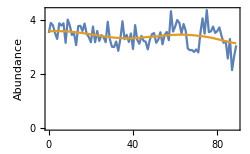
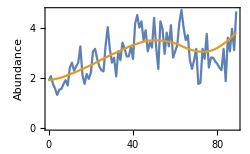

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.126811,0.349431}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0371762,0.120319}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.232286,0.262365}

```mathematica
(* fold weights *)
{aicFoldChlor[[dNum]],aicFoldBrach[[dNum]]}
```

{0.409649,0.883777}

```mathematica
(* hopf weights *)
{aicHopfChlor[[dNum]],aicHopfBrach[[dNum]]}
```

{0.000040211,0.116046}

```mathematica
psChlor[[14]]//Dimensions
```

{2,41}

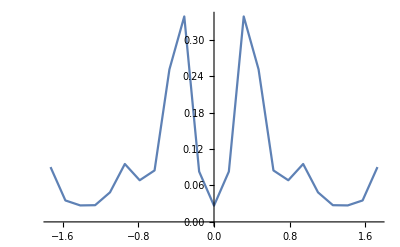

```mathematica
ListLinePlot[Transpose[psChlor[[14,;;,10;;-10]]],PlotRange->All]
```

```mathematica
TBFitSpec[psChlor[[14,;;,10;;-10]],0.25]
```

{6.79473×10^-7,0.999999,3.37904×10^-8}

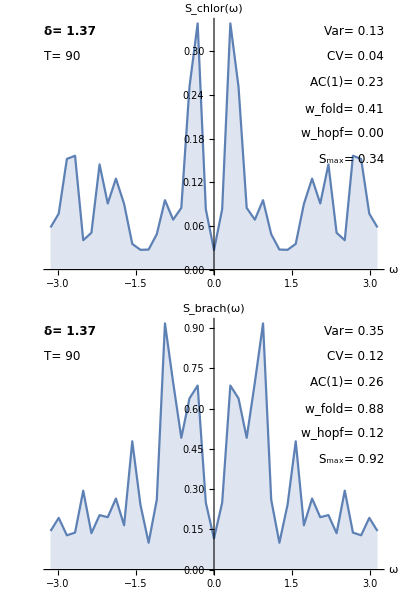

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=1.24

```mathematica
dNum=13;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

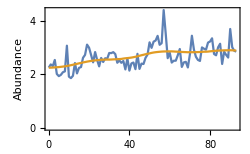
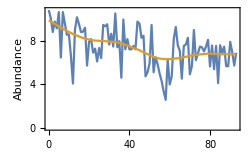

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.127301,2.321}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0479087,0.313762}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.403734,0.0993625}

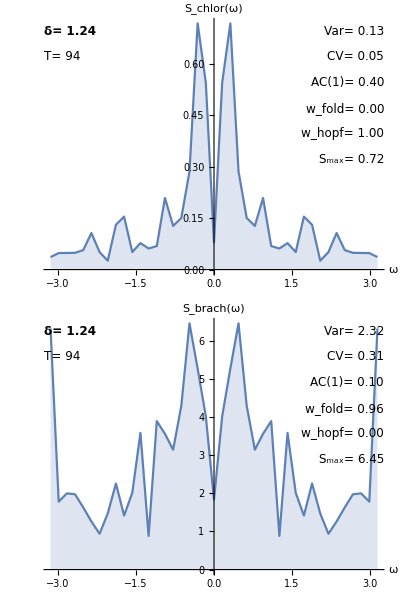

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=1.17

```mathematica
dNum=12;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

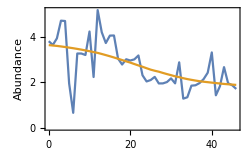
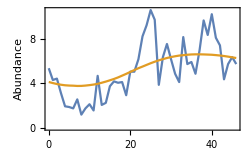

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.614376,3.51672}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.226249,0.674292}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.237771,0.5472}

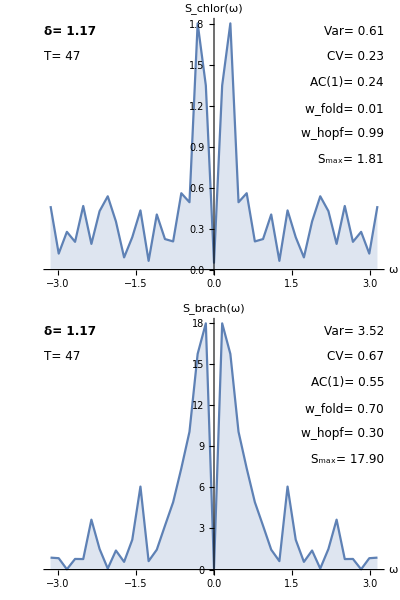

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=1.15

```mathematica
dNum=11;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

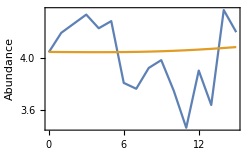
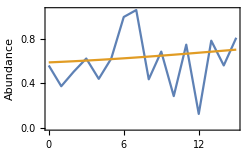

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0751494,0.0613103}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0187376,0.10171}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.428347,-0.123633}

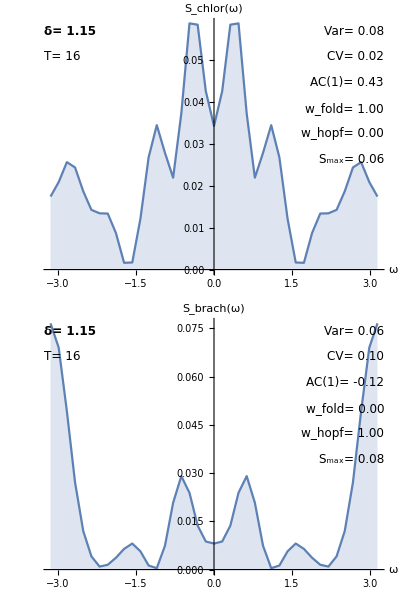

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=1.00

```mathematica
dNum=10;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

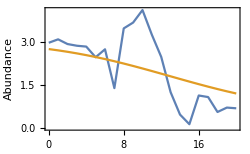
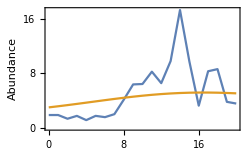

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.852393,13.1396}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.402072,2.52098}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.653475,0.545623}

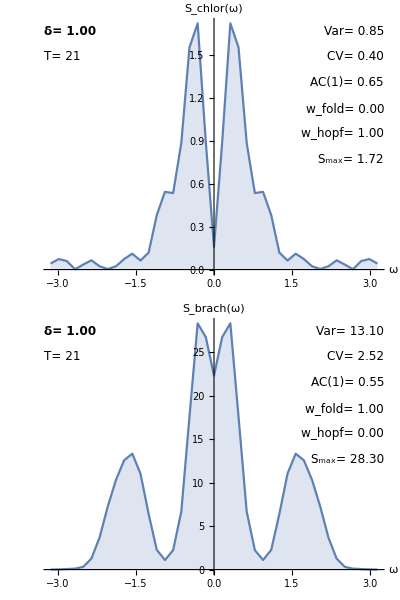

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.95

```mathematica
dNum=9;
plot=joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

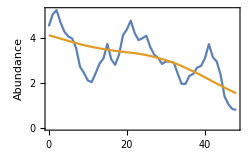
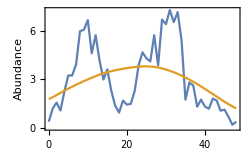

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.585863,3.19585}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.188684,1.0146}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.847593,0.787201}

```mathematica
TBFitSpec[psChlor[[9]],0.1]
```

{2.51489×10^-26,1.,1.52062×10^-31}

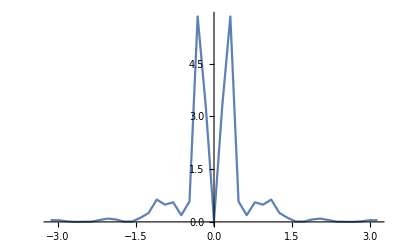

```mathematica
ListLinePlot[Transpose[psChlor[[9]]],PlotRange->All]
```

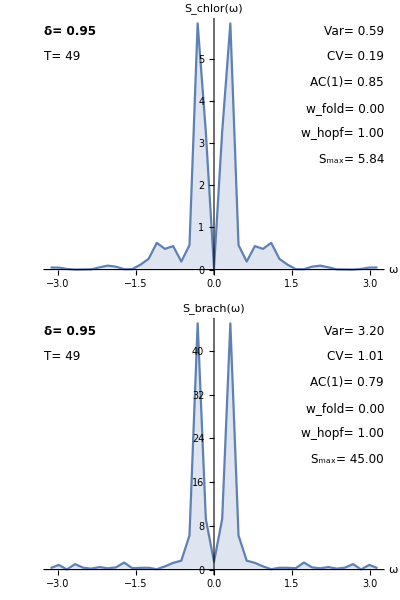

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.89

```mathematica
dNum=8;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

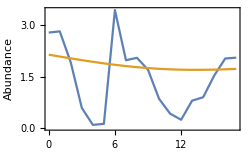
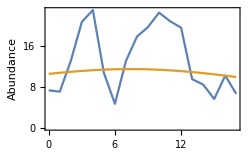

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.943747,37.8228}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.646156,2.83288}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.39112,0.536696}

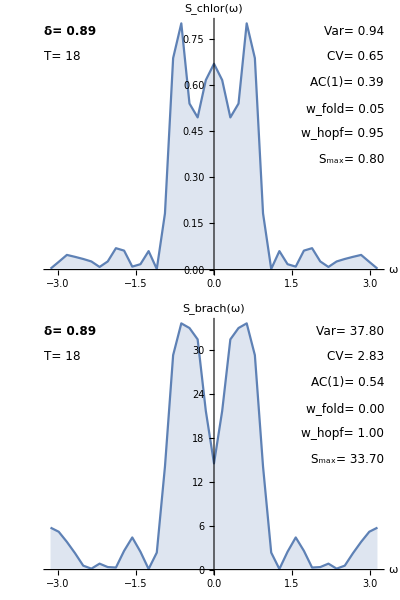

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.69

```mathematica
dNum=7;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

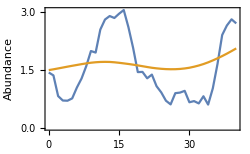
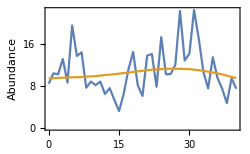

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.562227,18.2924}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.362727,1.68792}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.911204,0.302492}

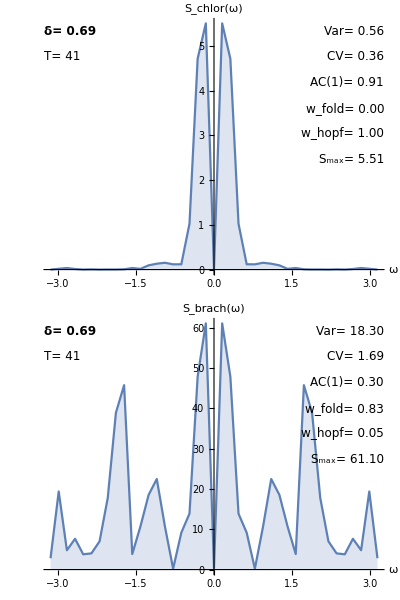

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.67

```mathematica
dNum=6;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

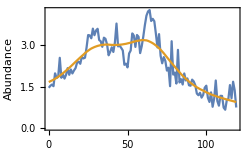
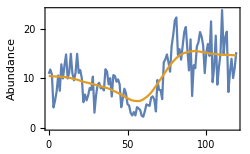

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.159309,10.6625}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0693849,0.99953}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.481751,0.313848}

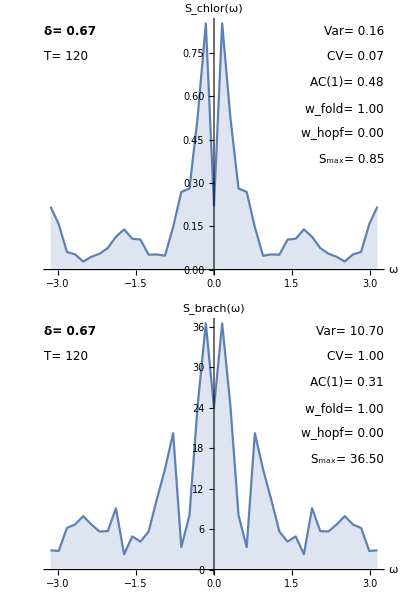

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.64

```mathematica
dNum=5;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

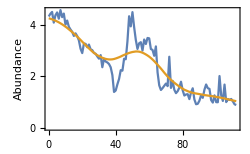
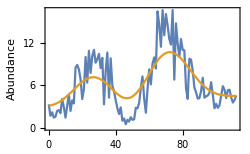

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.202879,6.20184}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0823051,0.987784}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.695711,0.424995}

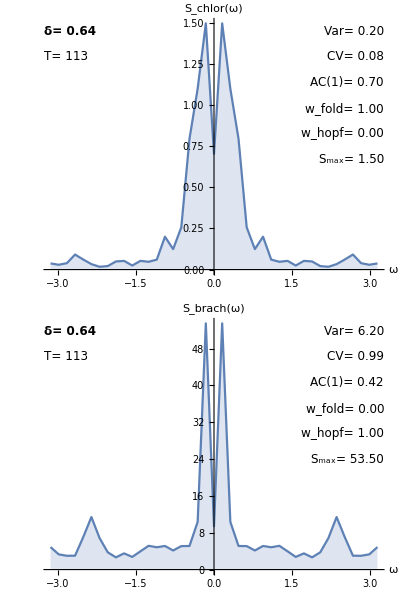

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.32

```mathematica
dNum=4;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

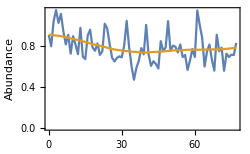
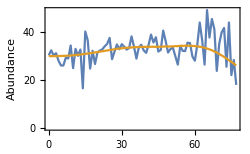

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0174318,28.3647}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0222971,0.8703}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.275546,-0.0485641}

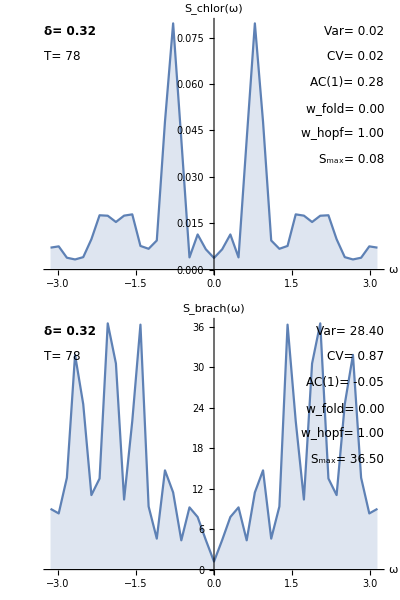

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.12

```mathematica
dNum=3;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

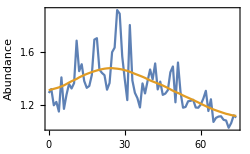
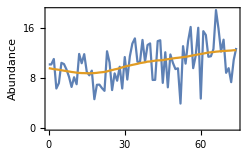

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0180072,7.74683}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0134985,0.749026}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.340764,0.04364}

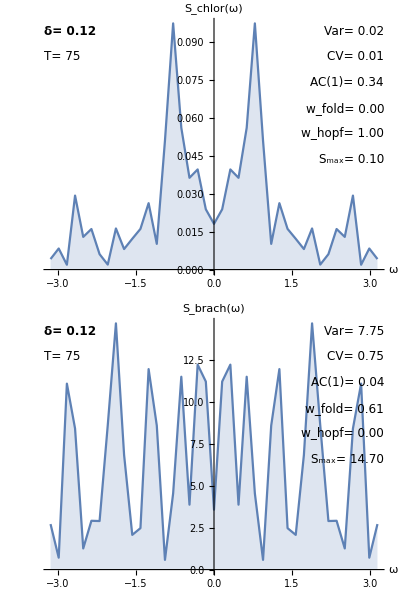

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.07

```mathematica
dNum=2;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

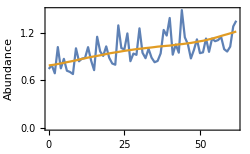
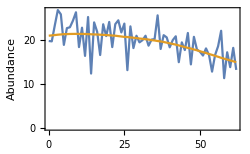

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0213872,9.20274}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0217562,0.467076}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.0403634,-0.364912}

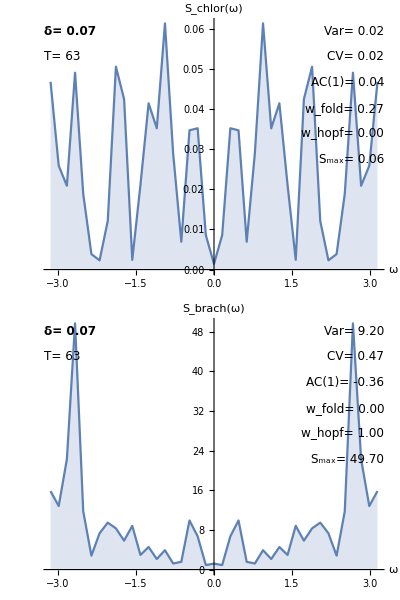

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### δ=0.04

```mathematica
dNum=1;
joinPlot[dNum]
```

-Graphics--Graphics-

```mathematica
(* ews data has form (fitplot,var,ac,pSpec) *)
ewsDataChlorella=ews[bandWidth,dataSet[[dNum,;;,2]],dataSet[[dNum,;;,1]]];
ewsDataBrach=ews[bandWidth,dataSet[[dNum,;;,3]],dataSet[[dNum,;;,1]]];
```

```mathematica
{lenChlor[[dNum]],fitPlotChlor[[dNum]],varChlor[[dNum]],cvarChlor[[dNum]],acChlor[[dNum]],psChlor[[dNum]],aicFoldChlor[[dNum]],aicHopfChlor[[dNum]],smaxChlor[[dNum]],cfChlor[[dNum]]}=ewsDataChlorella;
{lenBrach[[dNum]],fitPlotBrach[[dNum]],varBrach[[dNum]],cvarBrach[[dNum]],acBrach[[dNum]],psBrach[[dNum]],aicFoldBrach[[dNum]],aicHopfBrach[[dNum]],smaxBrach[[dNum]],cfBrach[[dNum]]}=ewsDataBrach;
```

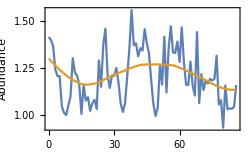
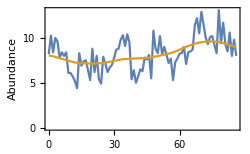

```mathematica
(* display fit plots *)
{fitPlotChlor[[dNum]],fitPlotBrach[[dNum]]}
```

```mathematica
(* variance *)
{varChlor[[dNum]],varBrach[[dNum]]}
```

{0.0155251,2.27817}

```mathematica
(* coefficient of variation *)
{cvarChlor[[dNum]],cvarBrach[[dNum]]}
```

{0.0128837,0.276764}

```mathematica
(* autocorrelation *)
{acChlor[[dNum]],acBrach[[dNum]]}
```

{0.429172,0.323209}

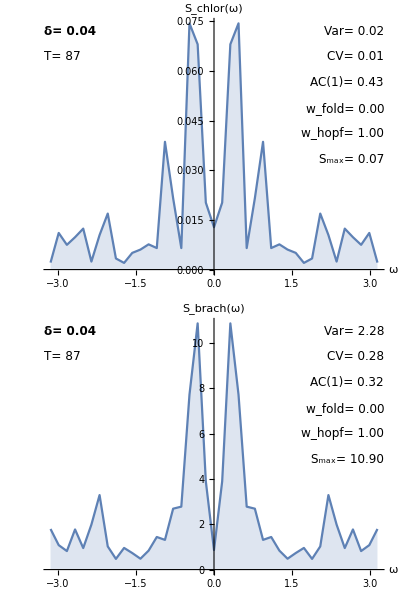

```mathematica
(* power spectra *)
psPlots[[dNum]]=psPlot[dNum,wmax]
```

### Playground

Compute AIC weights manually for a particular power spectrum to see what is going on with fits.

```mathematica
(*pSpec=psChlor[[14]];*)
```

```mathematica
(*ListLinePlot[Transpose[pSpec],PlotRange->All]*)
```

```mathematica
(*ψ=0.25;
ωMax=pSpec[[1,-1]];
Clear[ω0Thresh];
ω0Thresh[μ_,psi_]:=Sqrt[(μ^2/(4psi))(4-3psi + Sqrt[psi^2-16psi+16])];
(* fit power spectrum models to power spectrum *)
fitUnimodal=NonlinearModelFit[Transpose[pSpec],c*(1/(ω^2+λ^2)),{c,λ},ω];
fitBimodal=NonlinearModelFit[Transpose[pSpec],
{c*(1/((ω-ω0)^2+μ^2)+1/((ω+ω0)^2+μ^2)),μ<0,c>0,ωMax>ω0>ω0Thresh[μ,ψ]},{{ω0,0.4},{c,0.1},{μ,-1}},ω,
Method->"NMinimize"];
fitNull=NonlinearModelFit[Transpose[pSpec],c,{c},ω];*)
```

```mathematica
(*Plot[fitBimodal[x],{x,-3,3},PlotRange->All]*)
```

```mathematica
(*Show[Plot[{fitUnimodal[x],fitBimodal[x],fitNull[x]},{x,-Pi,Pi},PlotRange->All,PlotStyle->Black],
ListLinePlot[Transpose[pSpec],PlotRange->All]]*)
```

```mathematica
(*(* AIC scores from fitting *)
aicUnimodal=fitUnimodal["AIC"];
aicBimodal=fitBimodal["AIC"]//Quiet;
aicNull=fitNull["AIC"];

(* compute AIC deviations from best model *)
delUnimodal=aicUnimodal-Min[aicUnimodal,aicBimodal,aicNull];
delBimodal=aicBimodal-Min[aicUnimodal,aicBimodal,aicNull];
delNull=aicNull-Min[aicUnimodal,aicBimodal,aicNull];

(* compute relative likelihoods of each model *)
llhUnimodal=Exp[-(1/2)*delUnimodal];
llhBimodal=Exp[-(1/2)*delBimodal];
llhNull=Exp[-(1/2)*delNull];
llhTotal=Total[{llhUnimodal,llhBimodal,llhNull}];

(* normalise to get weights (all weight sum to 1) *)
weightUnimodal=llhUnimodal/llhTotal;
weightBimodal=llhBimodal/llhTotal;
weightNull=llhNull/llhTotal;
(* export the hopf weight and the rSquared ratio *)
{weightUnimodal,weightBimodal,weightNull}*)
```

### Plot of EWS statistics

```mathematica
ewsFramePlot=Grid[Partition[Table[psPlots[[i]],{i,1,Length[deltaVals]}],UpTo[3]],Spacings->{3,1},Frame->All]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Export["figures/empirical_ews_full.png",ewsFramePlot,ImageResolution->200];
```

### Overall statistics

```mathematica
NumberForm[deltaVals,{5,2}]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.89,0.95,1.00,1.15,1.17,1.24,1.37}

```mathematica
deltaValsRound=Table[NumberForm[deltaVals[[i]],{5,2}],{i,1,Length[deltaVals]}];
```

```mathematica
labels={"delta vals","var Chlor","var Brach","cvar Chlor","cvar Brach","ac Chlor","ac Brach"};
```

```mathematica
labels//TableForm
```

delta vals
var Chlor
var Brach
cvar Chlor
cvar Brach
ac Chlor
ac Brach

```mathematica
{deltaValsRound,varChlor,varBrach,cvarChlor,cvarBrach,acChlor,acBrach}//TableForm
```

0.04 | 0.07 | 0.12 | 0.32 | 0.64 | 0.67 | 0.69 | 0.89 | 0.95 | 1.00 | 1.15 | 1.17 | 1.24 | 1.37
0.0155251 | 0.0213872 | 0.0180072 | 0.0174318 | 0.202879 | 0.159309 | 0.562227 | 0.943747 | 0.585863 | 0.852393 | 0.0751494 | 0.614376 | 0.127301 | 0.126811
2.27817 | 9.20274 | 7.74683 | 28.3647 | 6.20184 | 10.6625 | 18.2924 | 37.8228 | 3.19585 | 13.1396 | 0.0613103 | 3.51672 | 2.321 | 0.349431
0.0128837 | 0.0217562 | 0.0134985 | 0.0222971 | 0.0823051 | 0.0693849 | 0.362727 | 0.646156 | 0.188684 | 0.402072 | 0.0187376 | 0.226249 | 0.0479087 | 0.0371762
0.276764 | 0.467076 | 0.749026 | 0.8703 | 0.987784 | 0.99953 | 1.68792 | 2.83288 | 1.0146 | 2.52098 | 0.10171 | 0.674292 | 0.313762 | 0.120319
0.429172 | 0.0403634 | 0.340764 | 0.275546 | 0.695711 | 0.481751 | 0.911204 | 0.39112 | 0.847593 | 0.653475 | 0.428347 | 0.237771 | 0.403734 | 0.232286
0.323209 | -0.364912 | 0.04364 | -0.0485641 | 0.424995 | 0.313848 | 0.302492 | 0.536696 | 0.787201 | 0.545623 | -0.123633 | 0.5472 | 0.0993625 | 0.262365

```mathematica
varBrach
```

{2.27817,9.20274,7.74683,28.3647,6.20184,10.6625,18.2924,37.8228,3.19585,13.1396,0.0613103,3.51672,2.321,0.349431}